```mathematica
ra=10;
ri=3;
b1=0.257;
b2=0.336;
d1=0.365;
d2=0.549;
αn=0.028;
αm=0.147;

σ1[x_,a_,α_]:=1/(1+Exp[-(x-a)4/α])
σ2[x_,a_,b_,α_]:=σ1[x,a,α](1-σ1[x,b,α])
σm[x_,y_,m_,α_]:=x(1-σ1[m,0.5,α])+y σ1[m,0.5,α]
s[n_,m_]:=σ2[n,σm[b1,d1,m,αm],σm[b2,d2,m,αm],αn]*2-1
sGrad = Grad[s[n1,m1],{n1,m1}];
sLin[n0_,m0_]:=(sGrad/.{n1->n0,m1->m0}).({n,m}-{n0,m0})+s[n0,m0]

M=π ri^2;
NN=π(ra^2-ri^2);

m[f_]:=Integrate[f[#1+r Cos[θ],#2+r Sin[θ]]*r/M,{r,0,ri},{θ,0,2π}]&
n[f_]:=Integrate[f[#1+r Cos[θ],#2+r Sin[θ]]*r/NN,{r,ri,ra},{θ,0,2π}]&

S[f_]:=s[n[f][#],m[f][#]]&
SLin[f0_,f_]:=sLin[n[f0][#1,#2],m[f0][#1,#2],n[f][#1,#2],m[f][#1,#2]]&

u0[{x_,y_}]:=k
{eqUn,eqSt}=k/.NSolve[{s[k,k]==0,0<k<1},k]

f0[{x_,y_}]:=eqSt;

u1[{x_,y_}]:=eqSt+0.01Sin[x/ri*π]Sin[y/ri*π]
```

{0.257146,0.338604}

-Graphics3D-

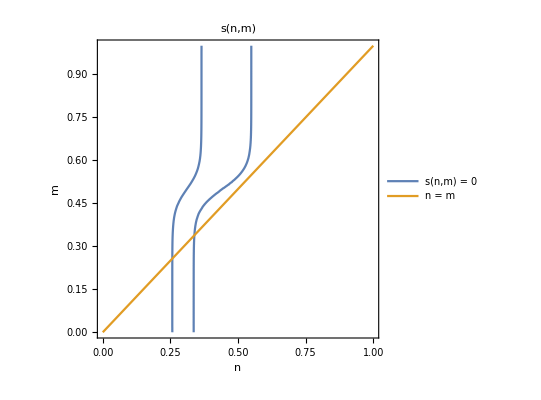

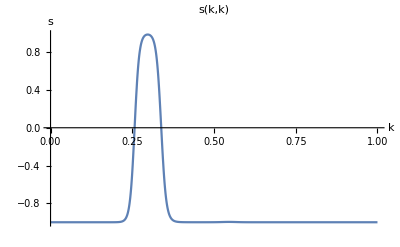

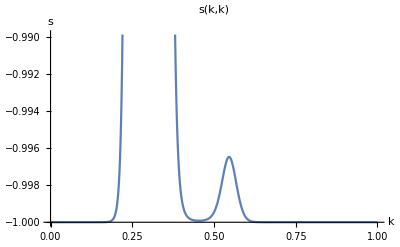

```mathematica
Plot3D[s[n,m],{n,0,1},{m,0,1},PlotRange->All,PlotPoints->60,PlotLabel->"s(n,m)",AxesLabel->{"n","m","s"}]
ContourPlot[{s[n,m]==0,n==m},{n,0,1},{m,0,1},PlotLabel->"s(n,m)",AxesLabel->{"n","m"},PlotLegends->{"s(n,m) = 0","n = m"}]
Plot[s[k,k],{k,0,1},PlotRange->All,PlotLabel->"s(k,k)",AxesLabel->{"k","s"}]
Plot[s[k,k],{k,0,1},PlotLabel->"s(k,k)",AxesLabel->{"k","s"}]
```

```mathematica
km[x_,y_]:=Piecewise[{{1/M,(x)^2+(y)^2≤ri^2},{0,True}}]
kn[x_,y_]:=Piecewise[{{1/NN,ri^2≤(x)^2+(y)^2≤ra^2},{0,True}}]

Plot3D[{km[x,y],kn[x,y]},{x,-ra,ra},{y,-ra,ra},PlotRange->{0.001,1/M+.001},PlotLabel->"Convolution kernels",PlotLegends->{"m","n"}]
f[x_,y_]:=Q+A Exp[I{a,b}.{x,y}+λ t]
Plot3D[Re[f[x,y]]/.{a->1,b->2,t->0,A->1,Q->0},{x,0,10},{y,0,10},PlotPoints->60,PlotLabel->"Eigenfunction of n and m: f(x,y)=e^(ⅈ (ax + by))"]
```

-Graphics3D-

-Graphics3D-

```mathematica
mf=InverseFourierTransform[FourierTransform[km[x,y],{x,y},{u,v}]*FourierTransform[f[x,y],{x,y},{u,v}],{u,v},{x,y}]*2π;
nf=InverseFourierTransform[FourierTransform[kn[x,y],{x,y},{u,v}]*FourierTransform[f[x,y],{x,y},{u,v}],{u,v},{x,y}]*2π;
λmf = Simplify[(mf/f[x,y])/.{Q->0}];
λnf=Simplify[(nf/f[x,y])/.{Q->0}];
mf//Expand//TraditionalForm
λmf//Expand//TraditionalForm
nf//Expand//TraditionalForm
λnf//Expand//TraditionalForm
```

Q+A 2-9/4 (a^2+b^2) ⅇ^(ⅈ a x+ⅈ b y+λ t)

2-9/4 (a^2+b^2)

100/91 A 2-25 (a^2+b^2) ⅇ^(ⅈ a x+ⅈ b y+λ t)-9/91 A 2-9/4 (a^2+b^2) ⅇ^(ⅈ a x+ⅈ b y+λ t)+Q

100/91 2-25 (a^2+b^2)-9/91 2-9/4 (a^2+b^2)

```mathematica
Plot3D[λnf,{a,-4,4},{b,-4,4},PlotPoints->100,MaxRecursion->0,PlotRange->All,PlotLabel->"Eigenvalues of n",AxesLabel->{"a","b","λ"}]
Plot3D[λmf,{a,-4,4},{b,-4,4},PlotPoints->60,MaxRecursion->2,PlotRange->All,PlotLabel->"Eigenvalues of m",AxesLabel->{"a","b","λ"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
tf=D[f[x,y],t];
λtf=D[f[x,y],t]/f[x,y];
rhs=sLin[eqSt,eqSt]/.{n->nf,m->mf}/.{Q->eqSt}//Expand;
rhs=rhs[[2;;]];(*get rid of the 10^-15)*)
lhs=tf;
lhs/f[x,y]/.Q->0
dispStable=rhs/f[x,y]/.Q->0//Simplify
dispStable/.{a^2+b^2->k^2}//TraditionalForm
Show@{
Plot3D[s[n,m],{n,0,1},{m,0,1},PlotRange->{-1,1},PlotStyle->Opacity[0.5],AxesLabel->{"n","m","s(n,m)"},PlotLabel->"Linearizing s around equilibrium"],
Plot3D[sLin[eqSt,eqSt],{n,m}∈Disk[{eqSt,eqSt},0.1],PlotTheme->"Minimal",PlotStyle->Blue]
}
```

λ

-78.4905 Hypergeometric0F1Regularized[2,-25 (a^2+b^2)]+12.0645 Hypergeometric0F1Regularized[2,-9/4 (a^2+b^2)]

12.0645 2-(9 k^2)/4-78.4905 2-25 k^2

-Graphics3D-

```mathematica
rhs=sLin[eqUn,eqUn]/.{n->nf,m->mf}/.{Q->eqSt}//Expand;
rhs=rhs[[2;;]];(*get rid of the 10^-15)*)
lhs/f[x,y]/.Q->0
dispUnstable=rhs/f[x,y]/.Q->0//Simplify
dispUnstable/.{a^2+b^2->k^2}//TraditionalForm
```

λ

78.49 Hypergeometric0F1Regularized[2,-25 (a^2+b^2)]-7.34653 Hypergeometric0F1Regularized[2,-9/4 (a^2+b^2)]

78.49 2-25 k^2-7.34653 2-(9 k^2)/4

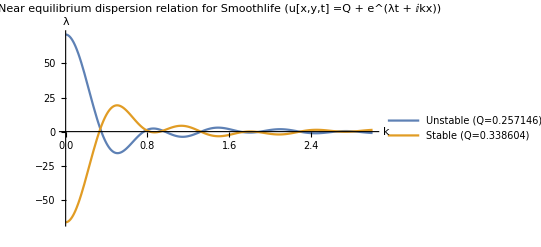

```mathematica
Plot[Evaluate@{dispUnstable,dispStable}/.{a^2+b^2->k^2}//Evaluate,{k,0,3},PlotRange->All,PlotLegends->{"Unstable (Q="<>ToString[eqUn]<>")","Stable (Q="<>ToString[eqSt]<>")"},PlotLabel->"Near equilibrium dispersion relation for Smoothlife (u[x,y,t] =Q + e^(λt  +  ⅈkx))",AxesLabel->{"k","λ"}]
```